```mathematica
Quit[]
```

```mathematica
SetDirectory[NotebookDirectory[]];
a = ReadList["plot2pi.txt", {Number,Number}];
b = ReadList["plot3pi.txt", {Number,Number}];
c = ReadList["plot4pi.txt", {Number,Number}];
d = ReadList["plot5pi.txt", {Number,Number}];
```

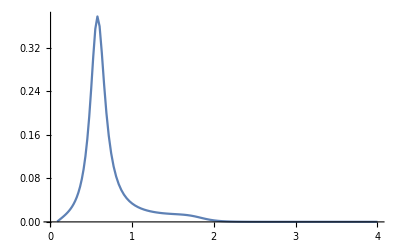

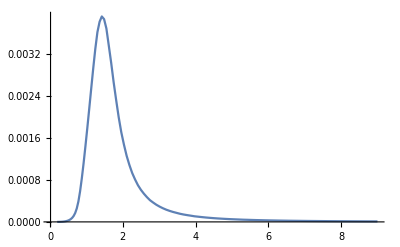

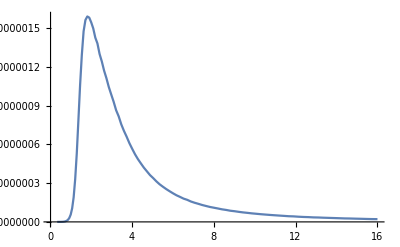

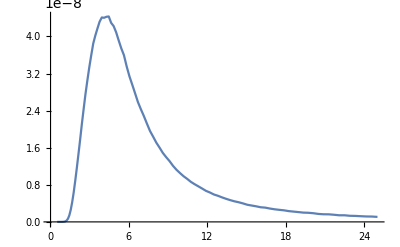

```mathematica
ListPlot[a, Joined->True, PlotRange->All]
ListPlot[b, Joined->True, PlotRange->All]
ListPlot[c, Joined->True, PlotRange->All]
ListPlot[d, Joined->True, PlotRange->All]
```

```mathematica
BWr[qsum_]:=Module[{ret,mRho,gammaRho,mRhopr,gammaRhopr,beta,m1,m2,mQ2,dRho,pPiRho,dRhopr,pPiRhopr,dQ,pPiQ,BRhoDem,BRho,BRhoprDem,BRhopr},mRho=0.775;
gammaRho=0.149;
mRhopr=1.364;
gammaRhopr=0.400;
beta=-0.108;
m1=0.13957018;m2=0.13957018;
mQ2=qsum*qsum;
dRho=mRho*mRho-m1*m1-m2*m2;
pPiRho=(1.0/mRho)*Sqrt[(dRho*dRho)/4.0-m1*m1*m2*m2];
dRhopr=mRhopr*mRhopr-m1*m1-m2*m2;
pPiRhopr=(1.0/mRhopr)*Sqrt[(dRhopr*dRhopr)/4.0-m1*m1*m2*m2];
dQ=mQ2-m1*m1-m2*m2;
pPiQ=(1.0/Sqrt[mQ2])*Sqrt[(dQ*dQ)/4.0-m1*m1*m2*m2];
gammaRho=gammaRho*mRho/Sqrt[mQ2]*Power[(pPiQ/pPiRho),3];
BRhoDem=mRho*mRho-mQ2+I*(-1.0*mRho*gammaRho);
BRho=mRho*mRho/BRhoDem;
gammaRhopr=gammaRhopr*mRhopr/Sqrt[mQ2]*Power[(pPiQ/pPiRhopr),3];
BRhoprDem=mRhopr*mRhopr-mQ2+I*(-1.0*mRho*gammaRhopr);
BRhopr=mRhopr*mRhopr/BRhoprDem;
ret=(BRho+beta*BRhopr)/(1+beta);
Return[ret]]
ret1=BWr[q]*Conjugate[BWr[q]];
mpi=0.13957018;
mπ=mpi;
ret2=ret1*(4*mpi^2-q*q);
ret3=ret2/(-3 q*q);
λr=Sqrt[(q^2-4 mpi^2)/q^2];
ret4=ret3*λr/(8 π);
ret5=ret4/.{q->Sqrt[q2]};
Fq2π=ret5;
Fq3π=(0.000058592966004157997*(-0.17640000000000003+q2)^4*(1+1.510651725804281*^-105*q2+189.45911486214024*q2^2))/((0.48273650253772327+(-1.0373349238887504+q2)^2)^2*q2^4)/2;
Fq4π=(0.00017983715820604627*(-0.31360000000000005+q2)*(1+5.074780646730226*q2+8.631754238222705*q2^2))/((0.6162735882355033+(-1.834698151162789+q2)^2)^2*q2);
Fq5π=32*((q2-25*mπ^2)/q2)^10*(1-1.65*q2+0.69 q2^2)/((q2+2.21)^2-4.69)^3;
```

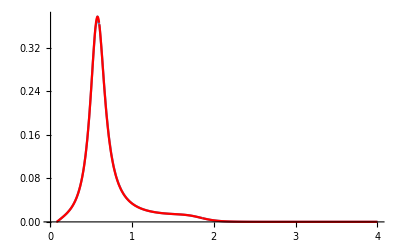

```mathematica
Show[ListPlot[a, Joined->True, PlotRange->All],Plot[Fq2π, {q2,4mpi^2,4 }, PlotRange->All, PlotStyle->Red]]
```

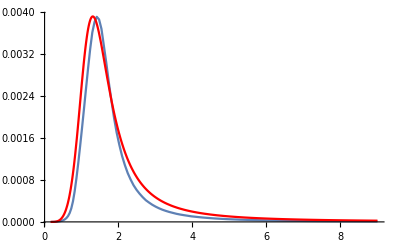

```mathematica
Show[ListPlot[b, Joined->True, PlotRange->All],Plot[Fq3π/4.4, {q2,9mpi^2,9 }, PlotRange->All, PlotStyle->Red], PlotRange-> All]
```

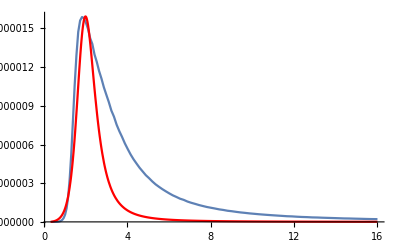

```mathematica
Show[ListPlot[c, Joined->True, PlotRange->All],Plot[Fq4π/10500, {q2,16mpi^2, 16 }, PlotRange->All, PlotStyle->Red], PlotRange-> All]
```

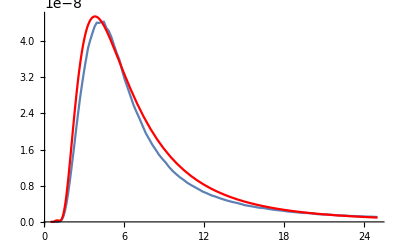

```mathematica
Show[ListPlot[d, Joined->True, PlotRange->All],Plot[Fq5π/27000, {q2,25mpi^2, 25}, PlotRange->All, PlotStyle->Red], PlotRange-> All]
```

```mathematica
Interpolation[a][4]
```

0.000105379